## 449 HW #6

#### 1) T 13.4

a) ψ''+k^2 ψ=U ψ where U=2m V/ℏ^2
Green’s function G''+k^2 G=δ(x-x')
ψ=ⅇ^(ⅈ k x)+∫ⅆ x'G(x,x')U(x')ψ(x')
ψ''+k^2 ψ=∫ⅆx'(G''(x,x')+k^2 G(x,x'))U(x')ψ(x')=∫ⅆx'(δ(x-x'))U(x')ψ(x')
=U(x)ψ(x)

b) G''+k^2 G=δ(x-x')
x>x' wave travelling to right → G_>=A ⅇ^(ⅈ k (x-x'))
x<x' wave travelling to left → G_<=A ⅇ^(-ⅈ k (x-x'))
integrate from x'-ϵ  to x'+ϵ :  G_>'-G_<'=1→ ⅈ k A-(-ⅈ k A)=1→ A=1/(2ⅈ k)
so G=1/(2 ⅈ k)ⅇ^(ⅈ k (x_>-x_<))

c) Born approx
ψ=ⅇ^(ⅈ k x)+∫ⅆ x'G(x,x')U(x')ⅇ^(ⅈ k x') so at large negative x we have
ψ=ⅇ^(ⅈ k x)+∫ⅆ x' 1/(2ⅈ k) ⅇ^(-ⅈ k (x-x'))U(x')ⅇ^(ⅈ k x')=ⅇ^(ⅈ k z)+ⅇ^(-ⅈ k x)∫ⅆ x' 1/(2ⅈ k) ⅇ^(2ⅈ k x')U(x')
so R=(|m/(ⅈ k ℏ^2)∫ⅆ x' ⅇ^(2ⅈ k x')V(x')|)^2

d) step of width a and height V_0

```mathematica
<<ThadStuff.m
```

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

```mathematica
r=(m Subscript[V, 0])/(ⅈ k ℏ^2)Integrate[ⅇ^(2ⅈ k x'),{x',0,a}]
```

-((-1+ⅇ^(2 ⅈ a k)) m V_0)/(2 k^2 ℏ^2)

```mathematica
R=SuperStar[r] r//FullSimplify
```

(m^2 Sin[a k]^2 V_0^2)/(k^4 ℏ^4)

```mathematica
(Series[1-1/(1+(U^2/(4 k^2 (k^2-U)))Sin[a √(k^2-U)]),{U,0,2}]//Normal//PowerExpand)/.U-> 2 m Subscript[V, 0]/ℏ^2
```

(m^2 Sin[a k] V_0^2)/(k^4 ℏ^4)

#### 2) T 13.7

f=-μ/(2π ℏ^2)∫V_0 ⅇ^(-r/a)ⅇ^(ⅈ q·r)d^3 r

```mathematica
Integrate[2π ⅇ^(ⅈ q r  Cos[θ])Sin[θ],{θ,0,π}]
```

(4 π Sin[q r])/(q r)

```mathematica
Integrate[(-μ V0)/(2 π ℏ^2)ⅇ^(-r/a)% r^2,{r,0,∞},Assumptions:>{a>0,q>0}]
```

-(4 a^3 V0 μ)/((ℏ+a^2 q^2 ℏ)^2)

```mathematica
((4 a^3 V0 μ)/((ℏ+a^2 q^2 ℏ)^2))^2/.q^2-> 4 k^2 Sin[th/2]^2
```

(16 a^6 V0^2 μ^2)/((ℏ+4 a^2 k^2 ℏ Sin[th/2]^2)^4)

So dσ/dΩ=|f|^2=(16 a^6 V0^2 μ^2)/((ℏ+4 a^2 k^2 ℏ Sin[th/2]^2)^4)

#### 3) T 13.12

r<a P_<=sin[k r]
r<a P_>= Sin[k r+δ] Sin[k a]/Sin[k a+δ]  (chosen so P is continuous at r=a)

first derivative P_>'-P_<'=γ P  so k Cos[k a+δ]Sin[k a]/Sin[k a+δ]-k Cos[k a]==γ Sin[k a] so
Cot[k a+δ]=γ/k+ Cot[k a]
Tan[k a+δ]=Tan[k a]/(γ/k+ Tan[k a])

low energies P_<=r,P_>=(a(r -A))/(a-A), a/(a-A)-1=γ a,  A=scattering length

```mathematica
Solve[a/(a-A)-1==γ a,A]
```

{{A→(a^2 γ)/(1+a γ)}}

so

```mathematica
4π A^2/.%
```

{(4 a^4 π γ^2)/(1+a γ)^2}

#### 4-5) By numerical integration of the Schrodinger equation, find the s-wave scattering length and the s-wave cross section as a function of energy for an electron scattering from the potential V(r)=-V_0/(1+(r/b)^6) for V_0= 9.5 eV, b=5 a_0. Plot your results from 0 to 10 eV, on a log-log scale. From your zero energy wavefunction, how many bound states are there in this potential?

work in atomic units

```mathematica
SE[e_]:=-1/2 p''[r]-(9.5/27.2)/(1+(r/5)^6)p[r]== e p[r];
```

```mathematica
p0[r_]=NDSolve[{SE[0],p[0]==0,p'[0]==1},p[r],{r,0,2000}]⟦1,1,2⟧
```

InterpolatingFunction[{{0., 2000.}}, <>][r]

```mathematica
NSolve[{p0[200]== c(200-a),p0'[200]==c },{c,a}]
```

{{c→0.0851397,a→32.4322}}

so zero energy cross section is

```mathematica
4π (32.4321807293958 .5292 Å)^2
```

3701.71 Å^2

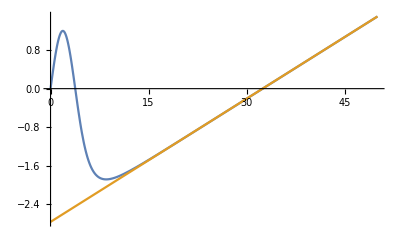

```mathematica
Plot[{p0[r],0.085139(r-32.43)},{r,0,50}]
```

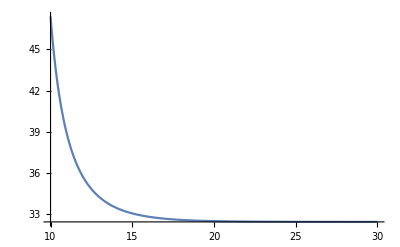

```mathematica
Plot[r-p0[r]/p0'[r],{r,10,30},PlotRange->All]
```

From the two zero crossings, we deduce that there are 2 bound states.

```mathematica
sm=30;δ[e_]:=Module[{k=√(2 e)},pk[s_]=NDSolve[{-1/2 p''[s]-(9.5/27.2)/(1+(s/5)^6)p[s]== e p[s],p[0]==0,p'[0]==1},p[s],{s,0,sm}]⟦1,1,2⟧;
Mod[ArcCot[pk'[sm]/(k pk[sm])]-k sm,π]]
```

```mathematica
es=10^Range[-6,2,.04];res=Table[{27.2e,(.5292)^2(4π)/(2 e)Sin[δ[e]]^2},{e,es}];
```

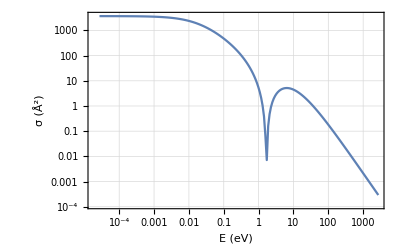

```mathematica
ThadPlot[ListLogLogPlot[res,Joined->True],{"E (eV)","σ (Å^2)"}]
```

#### 6) Find the equation that must be satisfied by the function G(r,r') in order that ψ_k(r̄)=ψ_k^0(r̄)+(2μ)/ℏ^2∫ⅆ^3 r̄'G(r̄,r̄')V(r̄')ψ_k(r̄') solves the Schrödinger equation for a particle of mass μ and energy E=(ℏ^2 k^2)/(2 μ). ψ_k^0(r̄) is a solution to the Schrödinger equation when V=0.

((∇_r)^2+k^2)(ψ_k^0(r)+(2μ)/ℏ^2∫ⅆ^3 r'G(r,r')V(r')ψ_k(r'))=0+(2μ)/ℏ^2∫ⅆ^3 r'[((∇_r)^2+k^2)G(r,r')]V(r')ψ_k(r')=(2μ)/ℏ^2 V(r)ψ_k(r)
This works if [((∇_r)^2+k^2)G(r,r')]=δ(r-r').